# Fitting Attentional Blink Data with Mathematica

(c) 2006, 2019

The following code is composed of a library ABFitting and this file showing how to use the library.

## a) Loading the library

```mathematica
Get[NotebookDirectory[]<>"ABFitting.m"]
```

Module ABFitting w/ LogLikelihood reparameterized loaded correctly. Type ? ABFitting for more.

```mathematica
? ABFitting
```

The ABFitting modules provides some functions that are used in Mathematica for fitting the Attentional Blink 
curve using a parameterized function to avoid parameter correlation. 
To load this module, use:

	 << path\ABFitting.m . 

The functions available are AB, LL and FitAB. 
It also provides tools for 
graphing the Attentional Blink curve. 
The functions available are PlotABData and PlotABCurve. 
Use ? name for more information.

## b) Setting some data

```mathematica
data={0.82,0.54,0.76,0.72,0.83,0.82,0.86,0.90};
```

Add before the percent correc the lag number, here consecutive numbers 1 to 8

```mathematica
paireddata={Range[8],data}ᵀ
```

{{1,0.82},{2,0.54},{3,0.76},{4,0.72},{5,0.83},{6,0.82},{7,0.86},{8,0.9}}

## c) Visualizing the theoretical curve from a set of parameters

The function AB returns the percent correct predicted for a given lag and from a set of parameters.

```mathematica
AB[1, {0.5, 1.0, .55, .35}]
```

0.683524

This function can be used in a Plot command....

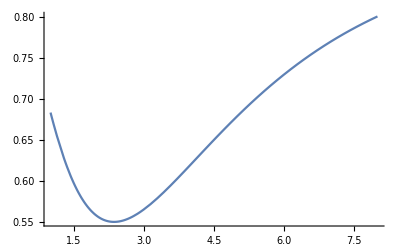

```mathematica
Plot[AB[x, {0.5, 1.0, .55, .35}], {x, 1, 8}]
```

... or you can use directly PlotABCurve with a list containing the four parameters to get the same result

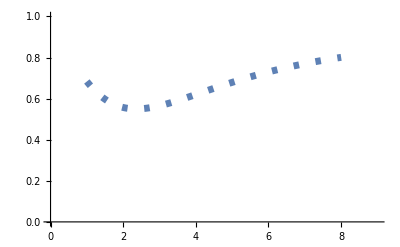

```mathematica
PlotABCurve[{0.5, 1.0, .55, .35}]
```

Other style can be provided.

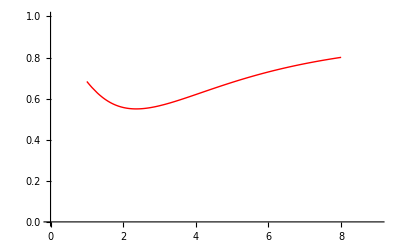

```mathematica
p1=PlotABCurve[{0.5, 1.0, .55, .35},PlotStyle->{Red,Thin}]
```

## d) Getting the log-likelihood index of fit

For a set of data composed of pairs {lag, percent correct}, and a set of parameters, you can look for the fit. Log-likelihood fits are always below zero, and the closer to zero are better fits.

```mathematica
LL[paireddata,{0.5, 1.0, .55, .35}]
```

-4.25786

## e) Find best-fitting parameters

The following functions find the best-fiting parameters, that is, those that makes the fit closest to zero:

```mathematica
sol=FitAB[paireddata]
```

{-3.99412,{l→0.269369,b→0.0858893,c→0.551678,d→0.323694}}

You can extract the four parameters from the above solution with

```mathematica
{l,b,c,d}/.sol⟦2⟧
```

{0.269369,0.0858893,0.551678,0.323694}

We can see the resulting predicted curve with

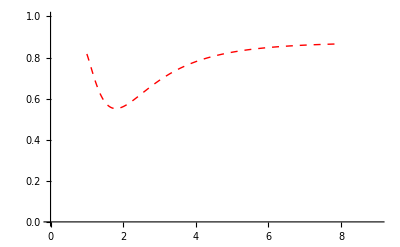

```mathematica
p1=PlotABCurve[{l,b,c,d}/.sol⟦2⟧,PlotStyle->{Dashed,Thin,Red}]
```

PlotABData plots the data only

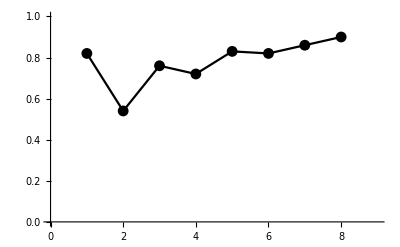

```mathematica
p2=PlotABData[paireddata,Mesh->All,PlotStyle->Black]
```

And this superimpose both plots

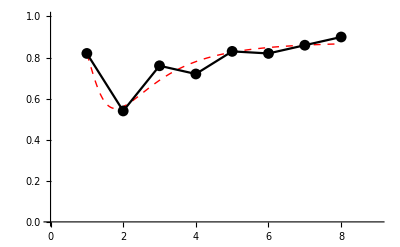

```mathematica
Show[p1,p2]
```